```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/guido/bispectrum_data

## Get data

```mathematica
datacmass=Import["numerics/Bis_ngc_cmass_g512_Dk6.txt","Table"];
datalowz=Import["numerics/Bis_ngc_lowz_g512_Dk6.txt","Table"];
```

We order the triangles as k1 > k2 > k3

```mathematica
tcmass=datacmass⟦All,{3,2,1}⟧;
tlowz=datacmass⟦All,{3,2,1}⟧;
```

```mathematica
{Length[tcmass],Length[tlowz]}
```

{825,825}

These are complex numbers, concatenated as floats

```mathematica
(*fftpow30temp=Import["numerics/fftpow_biasm0p25_Nmax30.dat","Table"]//Flatten;
re=fftpow30temp⟦;;;;2⟧;
im=fftpow30temp⟦2;;;;2⟧;
fftpow30=re+I im*)
```

## Final tables for Python

```mathematica
CtabB222=<<"tables/newCTab222.m";//AbsoluteTiming
CtabB3211=<<"tables/newCTab3211.m";//AbsoluteTiming
CtabB3212=<<"tables/newCTab3212_subk2.m";//AbsoluteTiming
CtabB411=<<"tables/newCTab411_subk2.m";//AbsoluteTiming
```

{0.322208,Null}

{12.557,Null}

{0.104947,Null}

{3.6995,Null}

Coefficients of bias combinations

```mathematica
coeffs222=<<"tables/coeffsb222.m";
coeffs3211=<<"tables/coeffsb3211.m";
coeffs3212=<<"tables/coeffsb3212_subk2.m";
coeffs411=<<"tables/coeffsb411_subk2.m";
```

```mathematica
coeffs222//Dimensions
```

{84,50}

List of bias combinations in front

```mathematica
b222list=<<"tables/biasb222list.m";
b3211list=<<"tables/biasb3211list.m";
b3212list=<<"tables/biasb3212list_subk2.m";
b411list=<<"tables/biasb411list_subk2.m";
```

So, which are the ones to marginalize over? For the biases we only have b1, b2, b5 not to marginalize over

```mathematica
b222list
```

{b1^2 f1,b1 f1^2,b1 b2 f1,b2 f1^2,b1 b5 f1,b5 f1^2,b1^2 f1^2,b1 f1^3,f1^3,f1^4,b1^3,b1^2 b2,b1^2 b5,b1^3 f1,b1 b2^2,b1 b2 b5,b1^2 b2 f1,b1 b2 f1^2,b1 b5^2,b1^2 b5 f1,b1 b5 f1^2,b1^3 f1^2,b1^2 f1^3,b1 f1^4,b2^3,b2^2 b5,b1 b2^2 f1,b2^2 f1,b2^2 f1^2,b2 b5^2,b1 b2 b5 f1,b2 b5 f1,b2 b5 f1^2,b1^2 b2 f1^2,b1 b2 f1^3,b2 f1^3,b2 f1^4,b5^3,b1 b5^2 f1,b5^2 f1,b5^2 f1^2,b1^2 b5 f1^2,b1 b5 f1^3,b5 f1^3,b5 f1^4,b1^3 f1^3,b1^2 f1^4,b1 f1^5,f1^5,f1^6}

```mathematica
b3211list
```

{b1^2 b2,b1^2 b5,b1^3,b1^2 b3,b1^2 b6,b1^2 b8,b1^2 b10,b1 b2^2,b1 b2 b3,b1 b2 b5,b1 b2 b6,b1 b2 b8,b1 b10 b2,b1 b3 b5,b1 b5^2,b1 b5 b6,b1 b5 b8,b1 b10 b5,b1^2 b2 f1,b1^2 b5 f1,b1^2 f1,b1^3 f1,b1^2 b3 f1,b1^2 b6 f1,b1^2 b8 f1,b1^2 b10 f1,b1 b2 f1,b1 b2^2 f1,b1 b2 b5 f1,b1 b5 f1,b1 b5^2 f1,b1 b3 f1,b1 b6 f1,b1 b8 f1,b1 b10 f1,b2^2 f1,b2 b3 f1,b2 b5 f1,b2 b6 f1,b2 b8 f1,b10 b2 f1,b3 b5 f1,b5^2 f1,b5 b6 f1,b5 b8 f1,b10 b5 f1,b1^2 b2 f1^2,b1^2 b5 f1^2,b1^2 f1^2,b1^3 f1^2,b1 b2 f1^2,b1 b5 f1^2,b1 f1^2,b1 b3 f1^2,b1 b6 f1^2,b1 b8 f1^2,b1 b10 f1^2,b2 f1^2,b2^2 f1^2,b2 b5 f1^2,b5 f1^2,b5^2 f1^2,b3 f1^2,b6 f1^2,b8 f1^2,b10 f1^2,b1^2 f1^3,b1^3 f1^3,b1 b2 f1^3,b1 b5 f1^3,b1 f1^3,b2 f1^3,b5 f1^3,f1^3,b3 f1^3,b6 f1^3,b8 f1^3,b10 f1^3,b1^2 f1^4,b1 f1^4,b2 f1^4,b5 f1^4,f1^4,b1 f1^5,f1^5,f1^6}

```mathematica
b3211list//Length
```

86

```mathematica
FortranForm[b3211list]
```

List(b1**2*b2,b1**2*b5,b1**3,b1**2*b3,b1**2*b6,b1**2*b8,b1**2*b10,b1*b2**2,
     -  b1*b2*b3,b1*b2*b5,b1*b2*b6,b1*b2*b8,b1*b10*b2,b1*b3*b5,b1*b5**2,b1*b5*b6,b1*b5*b8,
     -  b1*b10*b5,b1**2*b2*f1,b1**2*b5*f1,b1**2*f1,b1**3*f1,b1**2*b3*f1,b1**2*b6*f1,
     -  b1**2*b8*f1,b1**2*b10*f1,b1*b2*f1,b1*b2**2*f1,b1*b2*b5*f1,b1*b5*f1,b1*b5**2*f1,
     -  b1*b3*f1,b1*b6*f1,b1*b8*f1,b1*b10*f1,b2**2*f1,b2*b3*f1,b2*b5*f1,b2*b6*f1,b2*b8*f1,
     -  b10*b2*f1,b3*b5*f1,b5**2*f1,b5*b6*f1,b5*b8*f1,b10*b5*f1,b1**2*b2*f1**2,
     -  b1**2*b5*f1**2,b1**2*f1**2,b1**3*f1**2,b1*b2*f1**2,b1*b5*f1**2,b1*f1**2,
     -  b1*b3*f1**2,b1*b6*f1**2,b1*b8*f1**2,b1*b10*f1**2,b2*f1**2,b2**2*f1**2,b2*b5*f1**2,
     -  b5*f1**2,b5**2*f1**2,b3*f1**2,b6*f1**2,b8*f1**2,b10*f1**2,b1**2*f1**3,b1**3*f1**3,
     -  b1*b2*f1**3,b1*b5*f1**3,b1*f1**3,b2*f1**3,b5*f1**3,f1**3,b3*f1**3,b6*f1**3,
     -  b8*f1**3,b10*f1**3,b1**2*f1**4,b1*f1**4,b2*f1**4,b5*f1**4,f1**4,b1*f1**5,f1**5,
     -  f1**6)

```mathematica
b3212list
```

{b1^2 b2,b1^2 b5,b1^3,b1^2 b3,b1^2 b6,b1^2 b8,b1 b2^2,b1 b2 b3,b1 b2 b5,b1 b2 b6,b1 b2 b8,b1 b3 b5,b1 b5 b6,b1 b5 b8,b1^2 b2 f1,b1^2 b5 f1,b1^2 f1,b1^3 f1,b1^2 b3 f1,b1^2 b6 f1,b1^2 b8 f1,b1 b2 f1,b1 b5 f1,b1 b3 f1,b1 b6 f1,b1 b8 f1,b2^2 f1,b2 b3 f1,b2 b5 f1,b2 b6 f1,b2 b8 f1,b3 b5 f1,b5 b6 f1,b5 b8 f1,b1^2 b2 f1^2,b1^2 b5 f1^2,b1^2 f1^2,b1^3 f1^2,b1 b2 f1^2,b1 b5 f1^2,b1 f1^2,b1 b3 f1^2,b1 b6 f1^2,b1 b8 f1^2,b2 f1^2,b5 f1^2,b3 f1^2,b6 f1^2,b8 f1^2,b1^2 f1^3,b1^3 f1^3,b1 b2 f1^3,b1 b5 f1^3,b1 f1^3,b2 f1^3,b5 f1^3,f1^3,b3 f1^3,b6 f1^3,b8 f1^3,b1^2 f1^4,b1 f1^4,b2 f1^4,b5 f1^4,f1^4,b1 f1^5,f1^5,f1^6}

```mathematica
FortranForm[b3212list]
```

List(b1**2*b2,b1**2*b5,b1**3,b1**2*b3,b1**2*b6,b1**2*b8,b1*b2**2,b1*b2*b3,
     -  b1*b2*b5,b1*b2*b6,b1*b2*b8,b1*b3*b5,b1*b5*b6,b1*b5*b8,b1**2*b2*f1,b1**2*b5*f1,
     -  b1**2*f1,b1**3*f1,b1**2*b3*f1,b1**2*b6*f1,b1**2*b8*f1,b1*b2*f1,b1*b5*f1,b1*b3*f1,
     -  b1*b6*f1,b1*b8*f1,b2**2*f1,b2*b3*f1,b2*b5*f1,b2*b6*f1,b2*b8*f1,b3*b5*f1,b5*b6*f1,
     -  b5*b8*f1,b1**2*b2*f1**2,b1**2*b5*f1**2,b1**2*f1**2,b1**3*f1**2,b1*b2*f1**2,
     -  b1*b5*f1**2,b1*f1**2,b1*b3*f1**2,b1*b6*f1**2,b1*b8*f1**2,b2*f1**2,b5*f1**2,
     -  b3*f1**2,b6*f1**2,b8*f1**2,b1**2*f1**3,b1**3*f1**3,b1*b2*f1**3,b1*b5*f1**3,
     -  b1*f1**3,b2*f1**3,b5*f1**3,f1**3,b3*f1**3,b6*f1**3,b8*f1**3,b1**2*f1**4,b1*f1**4,
     -  b2*f1**4,b5*f1**4,f1**4,b1*f1**5,f1**5,f1**6)

```mathematica
b3212list//Length
```

68

```mathematica
b411list
```

{b1^3,b1^2 b2,b1^2 b3,b1^2 b4,b1^2 b5,b1^2 b6,b1^2 b7,b1^2 b8,b1^2 b9,b1^2 b11,b1^3 f1,b1^2 f1,b1^2 b2 f1,b1^2 b3 f1,b1^2 b5 f1,b1^2 b6 f1,b1^2 b8 f1,b1 b2 f1,b1 b3 f1,b1 b4 f1,b1 b5 f1,b1 b6 f1,b1 b7 f1,b1 b8 f1,b1 b9 f1,b1 b11 f1,b1^3 f1^2,b1^2 f1^2,b1^2 b2 f1^2,b1^2 b5 f1^2,b1 f1^2,b1 b2 f1^2,b1 b3 f1^2,b1 b5 f1^2,b1 b6 f1^2,b1 b8 f1^2,b2 f1^2,b3 f1^2,b4 f1^2,b5 f1^2,b6 f1^2,b7 f1^2,b8 f1^2,b9 f1^2,b11 f1^2,b1^3 f1^3,b1^2 f1^3,b1 f1^3,b1 b2 f1^3,b1 b5 f1^3,f1^3,b2 f1^3,b3 f1^3,b5 f1^3,b6 f1^3,b8 f1^3,b1^2 f1^4,b1 f1^4,f1^4,b2 f1^4,b5 f1^4,b1 f1^5,f1^5,f1^6}

```mathematica
FortranForm[b411list]
```

List(b1**3,b1**2*b2,b1**2*b3,b1**2*b4,b1**2*b5,b1**2*b6,b1**2*b7,b1**2*b8,
     -  b1**2*b9,b1**2*b11,b1**3*f1,b1**2*f1,b1**2*b2*f1,b1**2*b3*f1,b1**2*b5*f1,
     -  b1**2*b6*f1,b1**2*b8*f1,b1*b2*f1,b1*b3*f1,b1*b4*f1,b1*b5*f1,b1*b6*f1,b1*b7*f1,
     -  b1*b8*f1,b1*b9*f1,b1*b11*f1,b1**3*f1**2,b1**2*f1**2,b1**2*b2*f1**2,b1**2*b5*f1**2,
     -  b1*f1**2,b1*b2*f1**2,b1*b3*f1**2,b1*b5*f1**2,b1*b6*f1**2,b1*b8*f1**2,b2*f1**2,
     -  b3*f1**2,b4*f1**2,b5*f1**2,b6*f1**2,b7*f1**2,b8*f1**2,b9*f1**2,b11*f1**2,
     -  b1**3*f1**3,b1**2*f1**3,b1*f1**3,b1*b2*f1**3,b1*b5*f1**3,f1**3,b2*f1**3,b3*f1**3,
     -  b5*f1**3,b6*f1**3,b8*f1**3,b1**2*f1**4,b1*f1**4,f1**4,b2*f1**4,b5*f1**4,b1*f1**5,
     -  f1**5,f1**6)

```mathematica
bloop=Join[b222list,b3211list,b3212list,b411list];
```

```mathematica
biases={b1,b2,b3,b4,b5,b6,b7,b8,b9,b10,b11};
bgauss={b3,b4,b6,b7,b8,b9,b10,b11};
```

```mathematica
bun=MonomialList[Total[bloop//DeleteDuplicates],Flatten[{bgauss,{f1,b1,b2,b5}}]]
```

{b3 f1^3,b1 b3 f1^2,b3 f1^2,b1^2 b3 f1,b1 b3 f1,b2 b3 f1,b3 b5 f1,b1^2 b3,b1 b2 b3,b1 b3 b5,b4 f1^2,b1 b4 f1,b1^2 b4,b6 f1^3,b1 b6 f1^2,b6 f1^2,b1^2 b6 f1,b1 b6 f1,b2 b6 f1,b5 b6 f1,b1^2 b6,b1 b2 b6,b1 b5 b6,b7 f1^2,b1 b7 f1,b1^2 b7,b8 f1^3,b1 b8 f1^2,b8 f1^2,b1^2 b8 f1,b1 b8 f1,b2 b8 f1,b5 b8 f1,b1^2 b8,b1 b2 b8,b1 b5 b8,b9 f1^2,b1 b9 f1,b1^2 b9,b10 f1^3,b1 b10 f1^2,b10 f1^2,b1^2 b10 f1,b1 b10 f1,b10 b2 f1,b10 b5 f1,b1^2 b10,b1 b10 b2,b1 b10 b5,b11 f1^2,b1 b11 f1,b1^2 b11,f1^6,b1 f1^5,f1^5,b1^2 f1^4,b1 f1^4,b2 f1^4,b5 f1^4,f1^4,b1^3 f1^3,b1^2 f1^3,b1 b2 f1^3,b1 b5 f1^3,b1 f1^3,b2 f1^3,b5 f1^3,f1^3,b1^3 f1^2,b1^2 b2 f1^2,b1^2 b5 f1^2,b1^2 f1^2,b1 b2 f1^2,b1 b5 f1^2,b1 f1^2,b2^2 f1^2,b2 b5 f1^2,b2 f1^2,b5^2 f1^2,b5 f1^2,b1^3 f1,b1^2 b2 f1,b1^2 b5 f1,b1^2 f1,b1 b2^2 f1,b1 b2 b5 f1,b1 b2 f1,b1 b5^2 f1,b1 b5 f1,b2^2 f1,b2 b5 f1,b5^2 f1,b1^3,b1^2 b2,b1^2 b5,b1 b2^2,b1 b2 b5,b1 b5^2,b2^3,b2^2 b5,b2 b5^2,b5^3}

Look at the positions (in PYTHON, so with a -1) where the gaussian biases are

```mathematica
pos1=Position[#,bun⟦44⟧]&/@{b222list,b3211list,b3212list,b411list}
```

{{},{{35}},{},{}}

```mathematica
Flatten[Position[#,bun⟦44⟧]&/@{b222list,b3211list,b3212list,b411list},2]
```

{35}

```mathematica
D[b222list,#]&/@bgauss
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Get positions and coefficients of the gaussian biases (in Python, with a -1)

```mathematica
Cases[Table[{i-1,D[b3211list⟦i⟧,b11]},{i,1,Length[b3211list]}],{_,Except[0]}]
```

{}

```mathematica
Cases[Table[{i-1,D[b3212list⟦i⟧,b11]},{i,1,Length[b3212list]}],{_,Except[0]}]
```

{}

```mathematica
Cases[Table[{i-1,D[b411list⟦i⟧,b11]},{i,1,Length[b411list]}],{_,Except[0]}]
```

{{9,b1^2},{25,b1 f1},{44,f1^2}}

Look at counterterms and stochastic

```mathematica
ctr1blist={b1^2 Subscript[c, 1],b1 b2 Subscript[c, 1],b1 b5 Subscript[c, 1],b1^2 f1 Subscript[c, 1],b1 f1 Subscript[c, 1],b2 f1 Subscript[c, 1],b5 f1 Subscript[c, 1],b1 f1^2 Subscript[c, 1],f1^2 Subscript[c, 1],f1^3 Subscript[c, 1],b1^2 Subscript[c, 2],b1 b2 Subscript[c, 2],b1 b5 Subscript[c, 2],b1^2 f1 Subscript[c, 2],b1 f1 Subscript[c, 2],b2 f1 Subscript[c, 2],b5 f1 Subscript[c, 2],b1 f1^2 Subscript[c, 2],f1^2 Subscript[c, 2],f1^3 Subscript[c, 2],b1^2 Subscript[c, 3],b1 b2 Subscript[c, 3],b1 b5 Subscript[c, 3],b1^2 f1 Subscript[c, 3],b1 f1 Subscript[c, 3],b2 f1 Subscript[c, 3],b5 f1 Subscript[c, 3],b1 f1^2 Subscript[c, 3],f1^2 Subscript[c, 3],f1^3 Subscript[c, 3]};
Length[ctr1blist]
```

30

```mathematica
ctr2blist={b1^2 Subscript[c, 1],b1 f1 Subscript[c, 1],f1^2 Subscript[c, 1],b1^2 Subscript[c, 2],b1 f1 Subscript[c, 2],f1^2 Subscript[c, 2],b1^2 Subscript[c, 3],b1 f1 Subscript[c, 3],f1^2 Subscript[c, 3],b1^2 Subscript[c, 4],b1 f1 Subscript[c, 4],f1^2 Subscript[c, 4],b1^2 Subscript[c, 5],b1 f1 Subscript[c, 5],f1^2 Subscript[c, 5],b1^2 Subscript[c, 6],b1 f1 Subscript[c, 6],f1^2 Subscript[c, 6],b1^2 Subscript[c, 7],b1 f1 Subscript[c, 7],f1^2 Subscript[c, 7],b1^2 Subscript[c, 8],b1 f1 Subscript[c, 8],f1^2 Subscript[c, 8],b1^2 Subscript[c, 9],b1 f1 Subscript[c, 9],f1^2 Subscript[c, 9],b1^2 Subscript[c, 10],b1 f1 Subscript[c, 10],f1^2 Subscript[c, 10],b1^2 Subscript[c, 11],b1 f1 Subscript[c, 11],f1^2 Subscript[c, 11],b1^2 Subscript[c, 12],b1 f1 Subscript[c, 12],f1^2 Subscript[c, 12],b1^2 Subscript[c, 13],b1 f1 Subscript[c, 13],f1^2 Subscript[c, 13],b1^2 Subscript[c, 14],b1 f1 Subscript[c, 14],f1^2 Subscript[c, 14],b1^2 Subscript[c, 15],b1 f1 Subscript[c, 15],f1^2 Subscript[c, 15],b1^2 Subscript[c, 16],b1 f1 Subscript[c, 16],f1^2 Subscript[c, 16],b1^2 Subscript[c, 17],b1 f1 Subscript[c, 17],f1^2 Subscript[c, 17],b1^2 Subscript[c, 18],b1 f1 Subscript[c, 18],f1^2 Subscript[c, 18]};
Length[ctr2blist]
```

54

```mathematica
st2blist={b1 Subscript[e, 1],f1 Subscript[e, 1],b1 f1 Subscript[e, 1],f1^2 Subscript[e, 1],b1 Subscript[e, 2],f1 Subscript[e, 2],b1 f1 Subscript[e, 2],f1^2 Subscript[e, 2],b1 f1^2 Subscript[e, 3],f1^3 Subscript[e, 3],b1 f1^3 Subscript[e, 3],f1^4 Subscript[e, 3],b1 f1^2 Subscript[e, 4],f1^3 Subscript[e, 4],b1 f1^3 Subscript[e, 4],f1^4 Subscript[e, 4],b1 Subscript[e, 5],f1 Subscript[e, 5],b1 Subscript[e, 6],f1 Subscript[e, 6],b1 Subscript[e, 7],f1 Subscript[e, 7],b1 Subscript[e, 8],f1 Subscript[e, 8],b1 f1 Subscript[e, 9],f1^2 Subscript[e, 9],b1 f1 Subscript[e, 10],f1^2 Subscript[e, 10],b1 f1 Subscript[e, 11],f1^2 Subscript[e, 11],b1 f1 Subscript[e, 12],f1^2 Subscript[e, 12]};
Length[st2blist]
```

32

Get the coefficients multiplying the biases

```mathematica
For[j=1,j≤3,j++,
Print[Cases[Table[{i-1,D[ctr1blist⟦i⟧,Subscript[c, j]]},{i,1,Length[ctr1blist]}],{_,Except[0]}]]]
```

{{0,b1^2},{1,b1 b2},{2,b1 b5},{3,b1^2 f1},{4,b1 f1},{5,b2 f1},{6,b5 f1},{7,b1 f1^2},{8,f1^2},{9,f1^3}}

{{10,b1^2},{11,b1 b2},{12,b1 b5},{13,b1^2 f1},{14,b1 f1},{15,b2 f1},{16,b5 f1},{17,b1 f1^2},{18,f1^2},{19,f1^3}}

{{20,b1^2},{21,b1 b2},{22,b1 b5},{23,b1^2 f1},{24,b1 f1},{25,b2 f1},{26,b5 f1},{27,b1 f1^2},{28,f1^2},{29,f1^3}}

```mathematica
For[j=1,j≤18,j++,
Print[Cases[Table[{i-1,D[ctr2blist⟦i⟧,Subscript[c, j]]},{i,1,Length[ctr2blist]}],{_,Except[0]}]]]
```

{{0,b1^2},{1,b1 f1},{2,f1^2}}

{{3,b1^2},{4,b1 f1},{5,f1^2}}

{{6,b1^2},{7,b1 f1},{8,f1^2}}

{{9,b1^2},{10,b1 f1},{11,f1^2}}

{{12,b1^2},{13,b1 f1},{14,f1^2}}

{{15,b1^2},{16,b1 f1},{17,f1^2}}

{{18,b1^2},{19,b1 f1},{20,f1^2}}

{{21,b1^2},{22,b1 f1},{23,f1^2}}

{{24,b1^2},{25,b1 f1},{26,f1^2}}

{{27,b1^2},{28,b1 f1},{29,f1^2}}

{{30,b1^2},{31,b1 f1},{32,f1^2}}

{{33,b1^2},{34,b1 f1},{35,f1^2}}

{{36,b1^2},{37,b1 f1},{38,f1^2}}

{{39,b1^2},{40,b1 f1},{41,f1^2}}

{{42,b1^2},{43,b1 f1},{44,f1^2}}

{{45,b1^2},{46,b1 f1},{47,f1^2}}

{{48,b1^2},{49,b1 f1},{50,f1^2}}

{{51,b1^2},{52,b1 f1},{53,f1^2}}

```mathematica
For[j=1,j≤12,j++,
Print[Cases[Table[{i-1,D[st2blist⟦i⟧,Subscript[e, j]]},{i,1,Length[st2blist]}],{_,Except[0]}]]]
```

{{0,b1},{1,f1},{2,b1 f1},{3,f1^2}}

{{4,b1},{5,f1},{6,b1 f1},{7,f1^2}}

{{8,b1 f1^2},{9,f1^3},{10,b1 f1^3},{11,f1^4}}

{{12,b1 f1^2},{13,f1^3},{14,b1 f1^3},{15,f1^4}}

{{16,b1},{17,f1}}

{{18,b1},{19,f1}}

{{20,b1},{21,f1}}

{{22,b1},{23,f1}}

{{24,b1 f1},{25,f1^2}}

{{26,b1 f1},{27,f1^2}}

{{28,b1 f1},{29,f1^2}}

{{30,b1 f1},{31,f1^2}}

```mathematica
Solve[{(b2+b5)/(√2)==c2,(b2-b5)/(√2)==c4},{b2,b5}]//FullSimplify
```

{{b2→(c2+c4)/(√2),b5→(c2-c4)/(√2)}}

#### B222

Dimensions are: kernel coefficients x length of biaslist. So we’ll put back the powers of the kernel integrals and PS. For 222 we have all 3 PS, so no need to put the fftpow! We put the bias in first position

```mathematica
b222list
```

{b1^2 f1,b1 f1^2,b1 b2 f1,b2 f1^2,b1 b5 f1,b5 f1^2,b1^2 f1^2,b1 f1^3,f1^3,f1^4,b1^3,b1^2 b2,b1^2 b5,b1^3 f1,b1 b2^2,b1 b2 b5,b1^2 b2 f1,b1 b2 f1^2,b1 b5^2,b1^2 b5 f1,b1 b5 f1^2,b1^3 f1^2,b1^2 f1^3,b1 f1^4,b2^3,b2^2 b5,b1 b2^2 f1,b2^2 f1,b2^2 f1^2,b2 b5^2,b1 b2 b5 f1,b2 b5 f1,b2 b5 f1^2,b1^2 b2 f1^2,b1 b2 f1^3,b2 f1^3,b2 f1^4,b5^3,b1 b5^2 f1,b5^2 f1,b5^2 f1^2,b1^2 b5 f1^2,b1 b5 f1^3,b5 f1^3,b5 f1^4,b1^3 f1^3,b1^2 f1^4,b1 f1^5,f1^5,f1^6}

```mathematica
realidx=Complement[Range[Length[b222list]],Position[b222list/.f1->0,0]//Flatten]
```

{11,12,13,15,16,19,25,26,30,38}

```mathematica
b222list⟦realidx⟧
```

{b1^3,b1^2 b2,b1^2 b5,b1 b2^2,b1 b2 b5,b1 b5^2,b2^3,b2^2 b5,b2 b5^2,b5^3}

```mathematica
coeffs222pow=Table[{CtabB222⟦i,1⟧,CtabB222⟦i,2⟧,CtabB222⟦i,3⟧,coeffs222⟦i,j⟧},{j,1,Length[b222list]},{i,1,Length[CtabB222]}];
```

```mathematica
coeffs222pow//Dimensions
```

{50,84,4}

Evaluate numerically

```mathematica
coeffs222simp=Simplify[#/.{y->(k3^2-k1^2-k2^2)/(2 k1 k2)}]&/@coeffs222pow;
```

```mathematica
coeffs222simp//Dimensions
```

{50,84,4}

```mathematica
coeffs222simp⟦2,10⟧
```

{0,2,1,1/(11760 k1^2 k2^2)(-24 k2^4 k3^2 (k2^2-k3^2)^2+k1^8 (5 k2^2+12 k3^2)+k1^2 (5 k2^2+13 k3^2) (k2^3-k2 k3^2)^2-k1^6 (5 k2^4+69 k2^2 k3^2+24 k3^4)+k1^4 (-5 k2^6-40 k2^4 k3^2+147 k2^2 k3^4+12 k3^6))}

```mathematica
coeffs222zero=Simplify[coeffs222simp/.{k2->k1,k3->k1}]/.k1->0
```

{{{0,0,0,9/28},{0,2,0,0},{0,1,0,0},{0,0,2,0},{0,2,2,0},{0,1,2,0},{0,-1,2,0},{0,-2,2,-3/56},{0,0,1,0},{0,2,1,0},{0,1,1,0},{0,-1,1,1/28},{0,2,-1,0},59,{-1,1,1,0},{-1,2,-1,-1/28},{-2,2,0,-3/56},{-2,0,2,-3/56},{-2,2,2,0},{-2,1,2,0},{-2,2,1,0},{-2,1,1,-1/28},{-3,2,2,0},{-3,1,2,0},{-3,2,1,0},{-4,2,2,0}},48,{1}}
 |  |  |  |

```mathematica
coeffs222num=Monitor[Table[coeffs222zero⟦b,c⟧//N,{b,1,Dimensions[coeffs222zero]⟦1⟧},{c,1,Dimensions[coeffs222zero]⟦2⟧}],{b,c}];//AbsoluteTiming
```

{0.093655,Null}

```mathematica
Export["tables/coeffsb222_renzero.h5",coeffs222num]
```

tables/coeffsb222_renzero.h5

Evaluate a table that is needed to renormalize the UV, at k1=k2=k3=10^-3

```mathematica
coeffs222num=Monitor[Table[coeffs222simp⟦b,c⟧/.{k1->0.0001,k2->0.0001,k3->0.0001}//N,{b,1,Dimensions[coeffs222simp]⟦1⟧},{c,1,Dimensions[coeffs222simp]⟦2⟧}],{b,c}];//AbsoluteTiming
```

{0.112394,Null}

```mathematica
Export["tables/coeffsb222_renk1em4.h5",coeffs222num]
```

tables/coeffsb222_renk1em4.h5

Notice that in the tcmass and tlow we have triangle1 < triangle2 < triangle3.

```mathematica
triangles=tcmass;
```

```mathematica
coeffs222num=Monitor[Table[coeffs222simp⟦b,c⟧/.{k1->triangles⟦k,1⟧,k2->triangles⟦k,2⟧,k3->triangles⟦k,3⟧}//N,{b,1,Dimensions[coeffs222simp]⟦1⟧},{c,1,Dimensions[coeffs222simp]⟦2⟧},{k,1 ,Length[triangles]}],{b,c,k}];//AbsoluteTiming
```

{43.6313,Null}

```mathematica
Export["tables/coeffsb222_numlowz.h5",coeffs222num]
```

tables/coeffsb222_numlowz.h5

#### B321-1

```mathematica
b3211list
```

{b1^2 b2,b1^2 b5,b1^3,b1^2 b3,b1^2 b6,b1^2 b8,b1^2 b10,b1 b2^2,b1 b2 b3,b1 b2 b5,b1 b2 b6,b1 b2 b8,b1 b10 b2,b1 b3 b5,b1 b5^2,b1 b5 b6,b1 b5 b8,b1 b10 b5,b1^2 b2 f1,b1^2 b5 f1,b1^2 f1,b1^3 f1,b1^2 b3 f1,b1^2 b6 f1,b1^2 b8 f1,b1^2 b10 f1,b1 b2 f1,b1 b2^2 f1,b1 b2 b5 f1,b1 b5 f1,b1 b5^2 f1,b1 b3 f1,b1 b6 f1,b1 b8 f1,b1 b10 f1,b2^2 f1,b2 b3 f1,b2 b5 f1,b2 b6 f1,b2 b8 f1,b10 b2 f1,b3 b5 f1,b5^2 f1,b5 b6 f1,b5 b8 f1,b10 b5 f1,b1^2 b2 f1^2,b1^2 b5 f1^2,b1^2 f1^2,b1^3 f1^2,b1 b2 f1^2,b1 b5 f1^2,b1 f1^2,b1 b3 f1^2,b1 b6 f1^2,b1 b8 f1^2,b1 b10 f1^2,b2 f1^2,b2^2 f1^2,b2 b5 f1^2,b5 f1^2,b5^2 f1^2,b3 f1^2,b6 f1^2,b8 f1^2,b10 f1^2,b1^2 f1^3,b1^3 f1^3,b1 b2 f1^3,b1 b5 f1^3,b1 f1^3,b2 f1^3,b5 f1^3,f1^3,b3 f1^3,b6 f1^3,b8 f1^3,b10 f1^3,b1^2 f1^4,b1 f1^4,b2 f1^4,b5 f1^4,f1^4,b1 f1^5,f1^5,f1^6}

So we need the following format for the master integral: J(n1, n2, n3, d1, d2, d3, k1, k2, k3)
Here n1, n2, n3 are the power laws of the integrand, as 1/q^(2 n1)1/(|k1+q|^(2 n2))1/(|k2-q|^(2 n3))
Then we have d1, d2, d3 as q^d1|k1+q|^d2|k2-q|^d3, having P(q)->q^ν, for the moment it’s just a placeholder.
Here we have 2 PS. Notice that we only have to keep track of the variable of the PS. This is for the 123 permutation

```mathematica
pow3211temp=CtabB3211⟦All,1;;3⟧;
```

```mathematica
pospk1=Position[-2 D[pow3211temp,ν1],1]⟦All,2⟧
pospk2=Position[-2 D[pow3211temp,ν2],1]⟦All,2⟧
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}

{3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
coeffs3211//Dimensions
```

{145,86}

So we keep track of the positions of the PS, the first two table elements will be pospk1, pospk2

```mathematica
coeffs3211pow=Table[{pospk1⟦i⟧,pospk2⟦i⟧,CtabB3211⟦i,1⟧,CtabB3211⟦i,2⟧,CtabB3211⟦i,3⟧,coeffs3211⟦i,j⟧},{j,1,Length[b3211list]},{i,1,Length[CtabB3211]}];
```

```mathematica
coeffs3211pow⟦85,All,6⟧
```

{(k2^5 (165 k1^19 y (3+4 y^2)+25+k1^8 (7+2 k2^7 k3^4 (70769+790302 y^2+520944 y^4))))/(97020 (k1^4+(k2^2-1)^2-2 k1^2 (k2^2+k3^2))^4),-(k2^5 (1))/1,141,1/1,-(k2^2 (35 k1^14 (1+8 y^2)+1+14+1+k1^8 (1)))/(32340 k1^2 (k1^4+1^2-1)^4)}
 |  |  |  |

```mathematica
coeffs3211simp=Simplify[#/.{y->(k3^2-k1^2-k2^2)/(2 k1 k2)}]&/@coeffs3211pow;
```

```mathematica
coeffs3211simp//Dimensions
```

{86,145,6}

```mathematica
coeffs3211simp⟦10,56⟧/.k1->0.002
```

{1,3,-ν1/2,-1,-ν2/2,71428.6}

Evaluate a table that is needed to renormalize the UV. We will need 4 conditions in real space, so choose a few triangles around k1=k2=k3=10^-3. For the moment, let’s pick just the constant (to multiply P(k1) + P(k2) + P(k3)) at the equilateral triangle.

```mathematica
coeffs3211num=Monitor[Table[Flatten@{coeffs3211simp⟦b,c,;;5⟧/.{ν1->0,ν2->0},Evaluate[coeffs3211simp⟦b,c,6⟧/.{k1->0.001,k2->0.001,k3->0.001}]}//N,{b,1,Dimensions[coeffs3211simp]⟦1⟧},{c,1,Dimensions[coeffs3211simp]⟦2⟧}],{b,c}];//AbsoluteTiming
```

{0.30338,Null}

```mathematica
Export["tables/coeffsb3211_renk1em3.h5",coeffs3211num]
```

tables/coeffsb3211_renk1em3.h5

```mathematica
triren={{0.001,0.001,0.001},{0.002,0.002,0.001},{0.002,0.0015,0.0015},{0.003,0.002,0.0015}};
```

```mathematica
coeffs3211num123=Monitor[Table[Flatten@{coeffs3211simp⟦b,c,;;5⟧/.{ν1->0,ν2->0},Evaluate[coeffs3211simp⟦b,c,6⟧/.{k1->triren⟦k,1⟧,k2->triren⟦k,2⟧,k3->triren⟦k,3⟧}]}//N,{b,1,Dimensions[coeffs3211simp]⟦1⟧},{c,1,Dimensions[coeffs3211simp]⟦2⟧},{k,1 ,Length[triren]}],{b,c,k}];//AbsoluteTiming
```

{0.851301,Null}

```mathematica
coeffs3211num132=Monitor[Table[Flatten@{coeffs3211simp⟦b,c,;;5⟧/.{ν1->0,ν2->0},Evaluate[coeffs3211simp⟦b,c,6⟧/.{k1->triren⟦k,1⟧,k2->triren⟦k,3⟧,k3->triren⟦k,2⟧}]}//N,{b,1,Dimensions[coeffs3211simp]⟦1⟧},{c,1,Dimensions[coeffs3211simp]⟦2⟧},{k,1 ,Length[triren]}],{b,c,k}];//AbsoluteTiming
```

{0.822395,Null}

```mathematica
Export["tables/trianglesb3211_renreal.h5",triren]
```

tables/trianglesb3211_renreal.h5

```mathematica
Export["tables/coeffsb3211_p123_renreal.h5",coeffs3211num123]
```

tables/coeffsb3211_p123_renreal.h5

```mathematica
Export["tables/coeffsb3211_p132_renreal.h5",coeffs3211num132]
```

tables/coeffsb3211_p132_renreal.h5

```mathematica
triangles=tlowz;
```

```mathematica
coeffs3211num=Monitor[Table[coeffs3211simp⟦b,c⟧/.{ν1->0,ν2->0}/.{k1->triangles⟦k,1⟧,k2->triangles⟦k,2⟧,k3->triangles⟦k,3⟧}//N,{b,1,Dimensions[coeffs3211simp]⟦1⟧},{c,1,Dimensions[coeffs3211simp]⟦2⟧},{k,1 ,Length[triangles]}],{b,c,k}];//AbsoluteTiming
```

{169.716,Null}

```mathematica
Export["tables/coeffsb3211_p123_numlowz.h5",coeffs3211num]
```

tables/coeffsb3211_p123_numlowz.h5

Let’s do the other permutations. We have all 6 permutations here. The position of the PS variables will not change, only the external legs

```mathematica
coeffs3211num213=Monitor[Table[coeffs3211simp⟦b,c⟧/.{ν1->0,ν2->0}/.{k1->triangles⟦k,2⟧,k2->triangles⟦k,1⟧,k3->triangles⟦k,3⟧}//N,{b,1,Dimensions[coeffs3211simp]⟦1⟧},{c,1,Dimensions[coeffs3211simp]⟦2⟧},{k,1 ,Length[triangles]}],{b,c,k}];//AbsoluteTiming
```

{173.114,Null}

```mathematica
Export["tables/coeffsb3211_p213_numlowz.h5",coeffs3211num213]
```

tables/coeffsb3211_p213_numlowz.h5

```mathematica
coeffs3211num231=Monitor[Table[coeffs3211simp⟦b,c⟧/.{ν1->0,ν2->0}/.{k1->triangles⟦k,2⟧,k2->triangles⟦k,3⟧,k3->triangles⟦k,1⟧}//N,{b,1,Dimensions[coeffs3211simp]⟦1⟧},{c,1,Dimensions[coeffs3211simp]⟦2⟧},{k,1 ,Length[triangles]}],{b,c,k}];//AbsoluteTiming
```

{171.391,Null}

```mathematica
Export["tables/coeffsb3211_p231_numlowz.h5",coeffs3211num231]
```

tables/coeffsb3211_p231_numlowz.h5

```mathematica
coeffs3211num321=Monitor[Table[coeffs3211simp⟦b,c⟧/.{ν1->0,ν2->0}/.{k1->triangles⟦k,3⟧,k2->triangles⟦k,2⟧,k3->triangles⟦k,1⟧}//N,{b,1,Dimensions[coeffs3211simp]⟦1⟧},{c,1,Dimensions[coeffs3211simp]⟦2⟧},{k,1 ,Length[triangles]}],{b,c,k}];//AbsoluteTiming
```

{173.476,Null}

```mathematica
Export["tables/coeffsb3211_p321_numlowz.h5",coeffs3211num321]
```

tables/coeffsb3211_p321_numlowz.h5

```mathematica
coeffs3211num312=Monitor[Table[coeffs3211simp⟦b,c⟧/.{ν1->0,ν2->0}/.{k1->triangles⟦k,3⟧,k2->triangles⟦k,1⟧,k3->triangles⟦k,2⟧}//N,{b,1,Dimensions[coeffs3211simp]⟦1⟧},{c,1,Dimensions[coeffs3211simp]⟦2⟧},{k,1 ,Length[triangles]}],{b,c,k}];//AbsoluteTiming
```

{192.155,Null}

```mathematica
Export["tables/coeffsb3211_p312_numlowz.h5",coeffs3211num312]
```

tables/coeffsb3211_p312_numlowz.h5

```mathematica
coeffs3211num132=Monitor[Table[coeffs3211simp⟦b,c⟧/.{ν1->0,ν2->0}/.{k1->triangles⟦k,1⟧,k2->triangles⟦k,3⟧,k3->triangles⟦k,2⟧}//N,{b,1,Dimensions[coeffs3211simp]⟦1⟧},{c,1,Dimensions[coeffs3211simp]⟦2⟧},{k,1 ,Length[triangles]}],{b,c,k}];//AbsoluteTiming
```

{190.354,Null}

```mathematica
Export["tables/coeffsb3211_p132_numlowz.h5",coeffs3211num132]
```

tables/coeffsb3211_p132_numlowz.h5

#### B321-2

```mathematica
b3212list
```

{b1^2 b2,b1^2 b5,b1^3,b1^2 b3,b1^2 b6,b1^2 b8,b1 b2^2,b1 b2 b3,b1 b2 b5,b1 b2 b6,b1 b2 b8,b1 b3 b5,b1 b5 b6,b1 b5 b8,b1^2 b2 f1,b1^2 b5 f1,b1^2 f1,b1^3 f1,b1^2 b3 f1,b1^2 b6 f1,b1^2 b8 f1,b1 b2 f1,b1 b5 f1,b1 b3 f1,b1 b6 f1,b1 b8 f1,b2^2 f1,b2 b3 f1,b2 b5 f1,b2 b6 f1,b2 b8 f1,b3 b5 f1,b5 b6 f1,b5 b8 f1,b1^2 b2 f1^2,b1^2 b5 f1^2,b1^2 f1^2,b1^3 f1^2,b1 b2 f1^2,b1 b5 f1^2,b1 f1^2,b1 b3 f1^2,b1 b6 f1^2,b1 b8 f1^2,b2 f1^2,b5 f1^2,b3 f1^2,b6 f1^2,b8 f1^2,b1^2 f1^3,b1^3 f1^3,b1 b2 f1^3,b1 b5 f1^3,b1 f1^3,b2 f1^3,b5 f1^3,f1^3,b3 f1^3,b6 f1^3,b8 f1^3,b1^2 f1^4,b1 f1^4,b2 f1^4,b5 f1^4,f1^4,b1 f1^5,f1^5,f1^6}

So we need the following format for the master integral: J(n1, n2, n3, d1, d2, d3, k1, k2, k3)
Here n1, n2, n3 are the power laws of the integrand, as 1/q^(2 n1)1/(|k1+q|^(2 n2))1/(|k2-q|^(2 n3))
Then we have d1, d2, d3 as q^d1|k1+q|^d2|k2-q|^d3, having P(q)->q^ν, for the moment it’s just a placeholder.
Notice that this particular diagram will only have P(q) in each kernel term, no matter the permutations.

```mathematica
pow3212temp=CtabB3212⟦All,1;;3⟧
```

{{(4-ν)/2,0,0},{(4-ν)/2,1,0},{(4-ν)/2,-1,0},{(4-ν)/2,-2,0},{(2-ν)/2,0,0},{(2-ν)/2,1,0},{(2-ν)/2,-1,0},{(2-ν)/2,-2,0},{-ν/2,0,0},{-ν/2,1,0},{-ν/2,-1,0},{1/2 (-2-ν),0,0},{1/2 (-2-ν),1,0},{1/2 (-4-ν),1,0}}

```mathematica
pospk=Position[-2 D[pow3212temp,ν],1]⟦All,2⟧
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
coeffs3212//Dimensions
```

{14,68}

```mathematica
coeffs3212pow=Table[{CtabB3212⟦i,1⟧,CtabB3212⟦i,2⟧,CtabB3212⟦i,3⟧,coeffs3212⟦i,j⟧},{j,1,Length[b3212list]},{i,1,Length[CtabB3212]}];
```

```mathematica
coeffs3212simp=Simplify[#/.{y->(k3^2-k1^2-k2^2)/(2 k1 k2)}]&/@coeffs3212pow;
```

```mathematica
coeffs3212simp//Dimensions
```

{68,14,4}

```mathematica
triangles=tlowz;
```

```mathematica
coeffs3212num=Monitor[Table[coeffs3212simp⟦b,c⟧/.{ν->0}/.{k1->triangles⟦k,1⟧,k2->triangles⟦k,2⟧,k3->triangles⟦k,3⟧}//N,{b,1,Dimensions[coeffs3212simp]⟦1⟧},{c,1,Dimensions[coeffs3212simp]⟦2⟧},{k,1 ,Length[triangles]}],{b,c,k}];//AbsoluteTiming
```

{23.8225,Null}

```mathematica
Export["tables/coeffsb3212_p123_numlowz.h5",coeffs3212num]
```

tables/coeffsb3212_p123_numlowz.h5

Let’s do the other permutations. We have all 6 permutations here

```mathematica
coeffs3212num213=Monitor[Table[coeffs3212simp⟦b,c⟧/.{ν->0}/.{k1->triangles⟦k,2⟧,k2->triangles⟦k,1⟧,k3->triangles⟦k,3⟧}//N,{b,1,Dimensions[coeffs3212simp]⟦1⟧},{c,1,Dimensions[coeffs3212simp]⟦2⟧},{k,1 ,Length[triangles]}],{b,c,k}];//AbsoluteTiming
```

{27.5975,Null}

```mathematica
Export["tables/coeffsb3212_p213_numlowz.h5",coeffs3212num213]
```

tables/coeffsb3212_p213_numlowz.h5

```mathematica
coeffs3212num231=Monitor[Table[coeffs3212simp⟦b,c⟧/.{ν->0}/.{k1->triangles⟦k,2⟧,k2->triangles⟦k,3⟧,k3->triangles⟦k,1⟧}//N,{b,1,Dimensions[coeffs3212simp]⟦1⟧},{c,1,Dimensions[coeffs3212simp]⟦2⟧},{k,1 ,Length[triangles]}],{b,c,k}];//AbsoluteTiming
```

{45.9736,Null}

```mathematica
Export["tables/coeffsb3212_p231_numlowz.h5",coeffs3212num231]
```

tables/coeffsb3212_p231_numlowz.h5

```mathematica
coeffs3212num321=Monitor[Table[coeffs3212simp⟦b,c⟧/.{ν->0}/.{k1->triangles⟦k,3⟧,k2->triangles⟦k,2⟧,k3->triangles⟦k,1⟧}//N,{b,1,Dimensions[coeffs3212simp]⟦1⟧},{c,1,Dimensions[coeffs3212simp]⟦2⟧},{k,1 ,Length[triangles]}],{b,c,k}];//AbsoluteTiming
```

{22.219,Null}

```mathematica
Export["tables/coeffsb3212_p321_numlowz.h5",coeffs3212num321]
```

tables/coeffsb3212_p321_numlowz.h5

```mathematica
coeffs3212num312=Monitor[Table[coeffs3212simp⟦b,c⟧/.{ν->0}/.{k1->triangles⟦k,3⟧,k2->triangles⟦k,1⟧,k3->triangles⟦k,2⟧}//N,{b,1,Dimensions[coeffs3212simp]⟦1⟧},{c,1,Dimensions[coeffs3212simp]⟦2⟧},{k,1 ,Length[triangles]}],{b,c,k}];//AbsoluteTiming
```

{21.903,Null}

```mathematica
Export["tables/coeffsb3212_p312_numlowz.h5",coeffs3212num312]
```

tables/coeffsb3212_p312_numlowz.h5

```mathematica
coeffs3212num132=Monitor[Table[coeffs3212simp⟦b,c⟧/.{ν->0}/.{k1->triangles⟦k,1⟧,k2->triangles⟦k,3⟧,k3->triangles⟦k,2⟧}//N,{b,1,Dimensions[coeffs3212simp]⟦1⟧},{c,1,Dimensions[coeffs3212simp]⟦2⟧},{k,1 ,Length[triangles]}],{b,c,k}];//AbsoluteTiming
```

{22.002,Null}

```mathematica
Export["tables/coeffsb3212_p132_numlowz.h5",coeffs3212num132]
```

tables/coeffsb3212_p132_numlowz.h5

#### B411

```mathematica
b411list
```

{b1^3,b1^2 b2,b1^2 b3,b1^2 b4,b1^2 b5,b1^2 b6,b1^2 b7,b1^2 b8,b1^2 b9,b1^2 b11,b1^3 f1,b1^2 f1,b1^2 b2 f1,b1^2 b3 f1,b1^2 b5 f1,b1^2 b6 f1,b1^2 b8 f1,b1 b2 f1,b1 b3 f1,b1 b4 f1,b1 b5 f1,b1 b6 f1,b1 b7 f1,b1 b8 f1,b1 b9 f1,b1 b11 f1,b1^3 f1^2,b1^2 f1^2,b1^2 b2 f1^2,b1^2 b5 f1^2,b1 f1^2,b1 b2 f1^2,b1 b3 f1^2,b1 b5 f1^2,b1 b6 f1^2,b1 b8 f1^2,b2 f1^2,b3 f1^2,b4 f1^2,b5 f1^2,b6 f1^2,b7 f1^2,b8 f1^2,b9 f1^2,b11 f1^2,b1^3 f1^3,b1^2 f1^3,b1 f1^3,b1 b2 f1^3,b1 b5 f1^3,f1^3,b2 f1^3,b3 f1^3,b5 f1^3,b6 f1^3,b8 f1^3,b1^2 f1^4,b1 f1^4,f1^4,b2 f1^4,b5 f1^4,b1 f1^5,f1^5,f1^6}

So we need the following format for the master integral: J(n1, n2, n3, d1, d2, d3, k1, k2, k3)
Here n1, n2, n3 are the power laws of the integrand, as 1/q^(2 n1)1/(|k1+q|^(2 n2))1/(|k2-q|^(2 n3))
Then we have d1, d2, d3 as q^d1|k1+q|^d2|k2-q|^d3, having P(q)->q^ν, for the moment it’s just a placeholder.
Here we have 1 integrated PS, but we need to keep track of the variable it depends on.

```mathematica
pow411temp=CtabB411⟦All,1;;3⟧;
```

```mathematica
pow411temp⟦;;10⟧
```

{{0,(4-ν)/2,1},{0,(2-ν)/2,1},{0,-ν/2,1},{0,1/2 (-2-ν),1},{0,0,(4-ν)/2},{0,1,(4-ν)/2},{0,-1,(4-ν)/2},{0,-2,(4-ν)/2},{0,0,(2-ν)/2},{0,1,(2-ν)/2}}

```mathematica
pospk=Position[-2 D[pow411temp,ν],1]⟦All,2⟧
```

{2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,2,2,3,3,2,2,2,3,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,2,2,2,2,2,3,3,3,3,3,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,2,3,3,2,2,2,3,3,3,3,3,3,3,3,3,3,2,2,2,3,3,3,3,3,3,3,3,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
coeffs411//Dimensions
```

{188,64}

So we keep track of the position of the PS, the first one element of the table will be pospk

```mathematica
coeffs411pow=Table[{pospk⟦i⟧,CtabB411⟦i,1⟧,CtabB411⟦i,2⟧,CtabB411⟦i,3⟧,coeffs411⟦i,j⟧},{j,1,Length[b411list]},{i,1,Length[CtabB411]}];
```

```mathematica
coeffs411simp=Simplify[#/.{y->(k3^2-k1^2-k2^2)/(2 k1 k2)}]&/@coeffs411pow;
```

```mathematica
coeffs411simp//Dimensions
```

{64,188,5}

```mathematica
coeffs411simp⟦4,20⟧
```

{3,0,1,-2-ν/2,(k1^4+(k2^2-k3^2)^2-k1^2 (2 k2^2+9 k3^2))/(1848 k1^2 k2^2 k3^2)}

```mathematica
triangles=tlowz;
```

```mathematica
coeffs411num=Monitor[Table[coeffs411simp⟦b,c⟧/.{ν->0}/.{k1->triangles⟦k,1⟧,k2->triangles⟦k,2⟧,k3->triangles⟦k,3⟧}//N,{b,1,Dimensions[coeffs411simp]⟦1⟧},{c,1,Dimensions[coeffs411simp]⟦2⟧},{k,1 ,Length[triangles]}],{b,c,k}];//AbsoluteTiming
```

{215.109,Null}

```mathematica
Export["tables/coeffsb411_p123_numlowz.h5",coeffs411num]
```

tables/coeffsb411_p123_numlowz.h5

Let’s do the other permutations. We only need 3 cyclic ones

```mathematica
coeffs411num231=Monitor[Table[coeffs411simp⟦b,c⟧/.{ν->0}/.{k1->triangles⟦k,2⟧,k2->triangles⟦k,3⟧,k3->triangles⟦k,1⟧}//N,{b,1,Dimensions[coeffs411simp]⟦1⟧},{c,1,Dimensions[coeffs411simp]⟦2⟧},{k,1 ,Length[triangles]}],{b,c,k}];//AbsoluteTiming
```

{204.789,Null}

```mathematica
Export["tables/coeffsb411_p231_numlowz.h5",coeffs411num231]
```

tables/coeffsb411_p231_numlowz.h5

```mathematica
coeffs411num312=Monitor[Table[coeffs411simp⟦b,c⟧/.{ν->0}/.{k1->triangles⟦k,3⟧,k2->triangles⟦k,1⟧,k3->triangles⟦k,2⟧}//N,{b,1,Dimensions[coeffs411simp]⟦1⟧},{c,1,Dimensions[coeffs411simp]⟦2⟧},{k,1 ,Length[triangles]}],{b,c,k}];//AbsoluteTiming
```

{221.183,Null}

```mathematica
Export["tables/coeffsb411_p312_numlowz.h5",coeffs411num312]
```

tables/coeffsb411_p312_numlowz.h5

### Check with FFTLog for matter

#### Linear Power Spectrum

```mathematica
plindat=Import["FFTLog/PlinPlanck_z0p56.dat"];
As=plindat⟦1,2⟧;
kb=plindat⟦1,1⟧;
pextra=Table[{10^(-10+( i-1) 0.2), As (10^(-10+ (i-1) 0.2)/kb)^0.965},{i,1,30}];
plindat2=Join[pextra,plindat];
plinus=Interpolation[plindat2];
plin=Interpolation[Log[plindat2]];
```

```mathematica
khigh=4000.;
pcut[k_]= Exp[plin[Log[k]]]Exp[-(k/khigh)];
Plin[k_]=pcut[k];
```

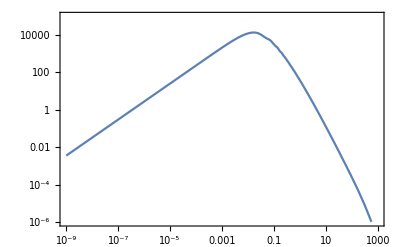

```mathematica
LogLogPlot[{Plin[k]},{k,10^-9,1000},Frame->True,PlotRange->{{0.000000001,1000},{10^-6,10^5}}]
```

#### Decomposition into power laws

```mathematica
(* Nmax lok k bins, form kmin to kmax *)
kBins[Nmax_,kmin_,kmax_]:=Module[{Δ,result},
Δ=1/(Nmax-1)Log[kmax/kmin]//N;
result=Table[kmin Exp[(i-1) Δ],{i,1,Nmax}];
result
];
```

```mathematica
(* A table of coefficents and powers in FFTLog decomposition of the linear power spectrum *)
CoeffPow[b_,Nmax_,k0_,kmax_]:=Module[{Δ,n,m,kn,ηm,ηn,Pn,cn,cnsym,result},
Δ=1/(Nmax-1)Log[kmax/k0]//N;
kn=Table[k0 Exp[(i-1) Δ],{i,1,Nmax}];
ηm=Table[b+(2π I)/(Nmax Δ)(j-Nmax/2-1),{j,1,Nmax+1}];

Pn=Table[{Plin[kn⟦i⟧]Exp[-b(i-1)Δ]},{i,1,Nmax}];
cn=Fourier[Pn,FourierParameters->{-1,-1}];
cnsym=Table[If[(j-Nmax/2)<1,k0^(-ηm⟦j⟧)Conjugate[cn⟦-j+Nmax/2+2,1⟧],k0^(-ηm⟦j⟧)cn⟦j-Nmax/2,1⟧],{j,1,Nmax+1}];
cnsym⟦1⟧=cnsym⟦1⟧/2;
cnsym⟦Length[cnsym]⟧=cnsym⟦Length[cnsym]⟧/2;
result=Table[{cnsym⟦i⟧,ηm⟦i⟧},{i,1,Length[ηm]}];
result
];
```

```mathematica
bias=-0.2501//N;
Nmax=24;
kmin=1. 10^-3;
kmax=1.;
cn=CoeffPow[bias,Nmax,kmin,kmax];
kn=kBins[Nmax,kmin,kmax];
```

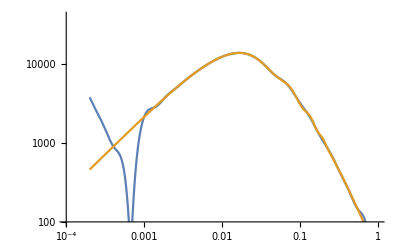

```mathematica
LogLogPlot[{Abs[Total[cn⟦All,1⟧k^cn⟦All,2⟧]],Plin[k]},{k,2 10^-4,1},PlotRange->{{10^-4,1},{100,40000}}]
```

#### Compiled J ( Not tested for Abs[Im[ν]]>10 )

```mathematica
(* Needs["CompiledFunctionTools`"];
CompilePrint[tildeFvec] *)
```

```mathematica
GammaC=Compile[{{z,_Complex}},
Block[{q0,q1,q2,q3,q4,q5,q6,p1,p2,result},
q0=75122.6331530+0.0I;
	q1=80916.6278952+0.0I;
	q2=36308.2951477+0.0I;
	q3=8687.24529705+0.0I;
	q4=1168.92649479+0.0I;
	q5=83.8676043424+0.0I;
	q6=2.50662827511+0.0I;
If[Re[z]≥0,p1=(q0+q1 z+q2 z^2+q3 z^3+q4 z^4+q5 z^5+q6 z^6)/(z(z+1)(z+2)(z+3)(z+4)(z+5)(z+6));result=p1 (z+5.5)^(z+0.5)Exp[-z-5.5],p1=(q0+q1(1-z)+q2 (1-z)^2+q3 (1-z)^3+q4 (1-z)^4+q5 (1-z)^5+q6 (1-z)^6)/((1-z)(2-z)(3-z)(4-z)(5-z)(6-z)(7-z));p2=p1(1-z+5.5)^(1-z+0.5)Exp[-1+z-5.5];result=π/(Sin[π z]p2)];
result
],
{{Sin[_],_Complex},{Exp[_],_Complex},{Re[_],_Real}}, 
CompilationTarget->"C",CompilationOptions->{"ExpressionOptimization" -> True,"InlineCompiledFunctions"->True,"InlineExternalDefinitions"->True},RuntimeOptions->{"CatchMachineOverflow"->False , "CatchMachineUnderflow"->False,"CatchMachineIntegerOverflow"->False,"CompareWithTolerance"->False,"EvaluateSymbolically"->False}];
```

```mathematica
Hyp2F1basic=Compile[{{a,_Complex},{b,_Complex},{c,_Complex},{z,_Complex}},
Block[{p,s,sold,eps,n},
s=0.0+0.0 I;
p=1.0+0.0I;
eps=1.0;
n=0.0;
While[eps>10^-12,
sold=s;
s=s+p;
p=p((a+n)(b+n))/((c+n)(n+1))z;
eps=Abs[(s-sold)/s];
n++];
s
],
CompilationTarget->"C",CompilationOptions->{"ExpressionOptimization" -> True,"InlineCompiledFunctions"->True,"InlineExternalDefinitions"->True},RuntimeOptions->{"CatchMachineOverflow"->False , "CatchMachineUnderflow"->False,"CatchMachineIntegerOverflow"->False,"CompareWithTolerance"->False,"EvaluateSymbolically"->False}];
```

```mathematica
JFastC = Compile[{{ν1,_Complex},{ν2,_Complex},{ν3,_Complex},{x,_Complex},{y,_Complex},{epscr,_Real}},
Block[
{p1,p2,s1,s2,s1old,s2old,eps,n,result},
s1=0.+I 0.;
p1=(GammaC[2-2 ν2] GammaC[2-2 ν3] Sin[π ν2] Sin[π ν3])/GammaC[5-2 ν2-2 ν3] x^(1.5-ν2-ν3);
p2=(GammaC[2-2 ν1] GammaC[2 (-2+ν1+ν2+ν3)] Sin[π ν1] Sin[π (ν1+ν2+ν3)])/GammaC[-1+2 ν2+2 ν3] y^(1.5-ν1-ν3);
s2=0.+I 0.;
eps=1.;
n=0.0;
While[eps>epscr,
s1old=s1;
s2old=s2;

s1=s1+p1 Hyp2F1basic[ν1+n,1.5-ν2+n,3-ν2-ν3+2 n,1-y];
s2=s2+p2 Hyp2F1basic[ν2+n,1.5-ν1+n,ν2+ν3+2 n,1-y];

p1=p1*((n+ν1) (3-ν1-ν2-ν3+n) (1.5-ν3+n) (1.5-ν2+n))/((1+n) (2.5-ν2-ν3+n) (4-ν2-ν3+2 n) (3-ν2-ν3+2 n)) x;
p2=p2*((1.5-ν1+n) (ν1+ν2+ν3-1.5+n) (n+ν2) (n+ν3))/((1+n) (ν2+ν3-0.5+n) (1+ν2+ν3+2 n) (ν2+ν3+2 n)) x;

eps=Abs[(s1-s2-s1old+s2old)/(s1-s2)];
n++];

result=Sec[π (ν2+ν3)]/(2 π^2) (s1-s2);
result
],
{{GammaC[_],_Complex},{Sec[_],_Complex},{Abs[_],_Real},{Sin[_],_Complex}}
,
CompilationTarget->"C",CompilationOptions->{"ExpressionOptimization" -> True,"InlineCompiledFunctions"->True,"InlineExternalDefinitions"->True},RuntimeOptions->{"CatchMachineOverflow"->False , "CatchMachineUnderflow"->False,"CatchMachineIntegerOverflow"->False,"CompareWithTolerance"->False,"EvaluateSymbolically"->False}];
```

#### B321-I

```mathematica
submat={f1->0,b1->1,b2->1,b3->1,b4->1,b5->0,b6->0,b7->0,b8->0,b9->0,b10->0,b11->0};
```

```mathematica
b3211listmat=b3211list/.submat
```

{1,0,1,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
coeffs3211mat=coeffs3211.b3211listmat;
coeffs3211mat//Dimensions
```

```mathematica
CtabB3211//Dimensions
```

{145,4}

Try the bad triangle, ordered

```mathematica
tri=tcmass⟦20⟧//Reverse
```

{0.220892,0.220892,0.017221}

```mathematica
Sum[(coeffs3211mat⟦i⟧/.Thread[{k1,k2,k3}->tri])JFastC[10^-10+CtabB3211⟦i,1⟧/.{ν1->cn⟦1,2⟧,ν2->cn⟦1,2⟧},10^-10+CtabB3211⟦i,2⟧/.{ν1->cn⟦1,2⟧,ν2->cn⟦1,2⟧},10^-10+CtabB3211⟦i,3⟧/.{ν1->cn⟦1,2⟧,ν2->cn⟦1,2⟧},(tri⟦3⟧/tri⟦1⟧)^2,(tri⟦2⟧/tri⟦1⟧)^2,10^-8],{i,1,Length[CtabB3211]}]
```

-0.0000513471-0.00027617 ⅈ

Do the table over i1 to Nmax+1, it’s double the time but it’s ok

```mathematica
Bn1n2n3step1=Table[
Sum[(coeffs3211mat⟦i⟧/.Thread[{k1,k2,k3}->tri])JFastC[10^-10+CtabB3211⟦i,1⟧/.{ν1->cn⟦i1,2⟧,ν2->cn⟦i2,2⟧},10^-10+CtabB3211⟦i,2⟧/.{ν1->cn⟦i1,2⟧,ν2->cn⟦i2,2⟧},10^-10+CtabB3211⟦i,3⟧/.{ν1->cn⟦i1,2⟧,ν2->cn⟦i2,2⟧},(tri⟦3⟧/tri⟦1⟧)^2,(tri⟦2⟧/tri⟦1⟧)^2,10^-8],{i,1,Length[CtabB3211]}],
{i1,1,Nmax+1},{i2,1,Nmax+1}];//AbsoluteTiming
```

{3.86669,Null}

```mathematica
D[CtabB3211⟦All,1⟧,ν1]
```

{-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Bn1n2n3step1⟦1⟧
```

{-0.0000513471-0.00027617 ⅈ,-0.000126301-0.0000232376 ⅈ,0.000141371-0.000130299 ⅈ,-0.000134518-0.000288229 ⅈ,-0.0000801675+0.0000613466 ⅈ,0.000187464-0.000233922 ⅈ,-0.000268016-0.000255227 ⅈ,0.0000579469+0.000167971 ⅈ,0.000184974-0.000464623 ⅈ,-0.000498857-0.000055146 ⅈ,0.00045732+0.000148258 ⅈ,-0.000524024-0.000559131 ⅈ,0.000910893+0.000158919 ⅈ,-0.000207412+0.00016034 ⅈ,0.000479011-0.00060989 ⅈ,-0.000595564-0.000311495 ⅈ,0.000105422+0.000188952 ⅈ,7.98848×10^-6-0.000433947 ⅈ,-0.000309828-5.09688×10^-6 ⅈ,0.000162382-0.0000347736 ⅈ,-0.000095969-0.000348719 ⅈ,-0.000124081+4.5007×10^-7 ⅈ,0.000182185-0.000111948 ⅈ,-0.000200731-0.000121091 ⅈ,-0.000448857+0.000037774 ⅈ}

```mathematica
cn⟦All,2⟧
```

{-0.2501-10.4602 ⅈ,-0.2501-9.58853 ⅈ,-0.2501-8.71685 ⅈ,-0.2501-7.84516 ⅈ,-0.2501-6.97348 ⅈ,-0.2501-6.10179 ⅈ,-0.2501-5.23011 ⅈ,-0.2501-4.35842 ⅈ,-0.2501-3.48674 ⅈ,-0.2501-2.61505 ⅈ,-0.2501-1.74337 ⅈ,-0.2501-0.871685 ⅈ,-0.2501+0. ⅈ,-0.2501+0.871685 ⅈ,-0.2501+1.74337 ⅈ,-0.2501+2.61505 ⅈ,-0.2501+3.48674 ⅈ,-0.2501+4.35842 ⅈ,-0.2501+5.23011 ⅈ,-0.2501+6.10179 ⅈ,-0.2501+6.97348 ⅈ,-0.2501+7.84516 ⅈ,-0.2501+8.71685 ⅈ,-0.2501+9.58853 ⅈ,-0.2501+10.4602 ⅈ}

```mathematica
cnc=tri⟦1⟧^(1.5+cn⟦All,2⟧)cn⟦All,1⟧;
b321fin=Plin[tri⟦1⟧]Re[Bn1n2n3step1.cnc.cnc]
```

-18199.4

```mathematica
Re[Bn1n2n3step1.cnc.cnc]
```

-20.3148

Need to add the permutations

```mathematica
cn⟦All,2⟧
```

{-0.2501-10.4602 ⅈ,-0.2501-9.58853 ⅈ,-0.2501-8.71685 ⅈ,-0.2501-7.84516 ⅈ,-0.2501-6.97348 ⅈ,-0.2501-6.10179 ⅈ,-0.2501-5.23011 ⅈ,-0.2501-4.35842 ⅈ,-0.2501-3.48674 ⅈ,-0.2501-2.61505 ⅈ,-0.2501-1.74337 ⅈ,-0.2501-0.871685 ⅈ,-0.2501+0. ⅈ,-0.2501+0.871685 ⅈ,-0.2501+1.74337 ⅈ,-0.2501+2.61505 ⅈ,-0.2501+3.48674 ⅈ,-0.2501+4.35842 ⅈ,-0.2501+5.23011 ⅈ,-0.2501+6.10179 ⅈ,-0.2501+6.97348 ⅈ,-0.2501+7.84516 ⅈ,-0.2501+8.71685 ⅈ,-0.2501+9.58853 ⅈ,-0.2501+10.4602 ⅈ}

```mathematica
Bn1n2n3step1=Table[
Sum[(coeffs3211mat⟦i⟧/.Thread[{k1,k2,k3}->tri])JFastC[10^-10+CtabB3211⟦i,1⟧/.{ν1->cn⟦i1,2⟧,ν2->cn⟦i2,2⟧},10^-10+CtabB3211⟦i,2⟧/.{ν1->cn⟦i1,2⟧,ν2->cn⟦i2,2⟧},10^-10+CtabB3211⟦i,3⟧/.{ν1->cn⟦i1,2⟧,ν2->cn⟦i2,2⟧},(tri⟦3⟧/tri⟦1⟧)^2,(tri⟦2⟧/tri⟦1⟧)^2,10^-8],{i,1,Length[CtabB3211]}],
{i1,1,Nmax+1},{i2,1,Nmax+1}];//AbsoluteTiming
```